```mathematica
f[s_,k_,t_]:=FinancialDerivative[{"European","Call"}, {"StrikePrice"->k, "Expiration"->t},  {"InterestRate"-> 0, "Volatility" -> 0.5, "CurrentPrice"-> s, "Dividend"->0}]
```

```mathematica
s[x_,t_]:=x*f[1,2-1/x,t]+x-1;l[x_,t_]:=x*f[1,1/x,t];
```

Plot::exclul: {(1 - x - x\ FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}] + x\ FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}]) - 0, (-1 + x + x\ « 1 » - x\ FinancialDerivative[« 1 »]) - 0} must be a list of equalities or real-valued functions.

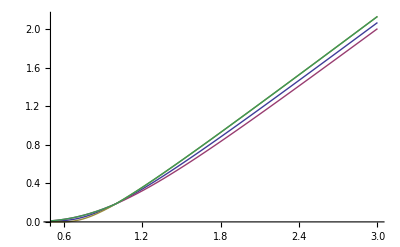

FinancialDerivative::checknumeric: parameters {"StrikePrice" → -0.042081} cannot have "negative" values

FinancialDerivative::checknumeric: parameters {"StrikePrice" → -0.0918418} cannot have "negative" values

General::stop: Further output of FinancialDerivative :: checknumeric will be suppressed during this calculation.

Plot::exclul: {(-1 + x - FinancialDerivative[{"European", "Call"}, {Rule[« 2 »], Rule[« 2 »]}, {Rule[« 2 »], Rule[« 2 »], Rule[« 2 »], Rule[« 2 »]}] + FinancialDerivative[{"European", "Call"}, {"StrikePrice" → Times[« 2 »], "Expiration" → 5}, {"InterestRate" → 0, "Volatility" → 0.5, "CurrentPrice" → 1, "Dividend" → 0}]) - 0, (1 - x + « 19 »[« 1 »] - FinancialDerivative[« 1 »]) - 0} must be a list of equalities or real-valued functions.

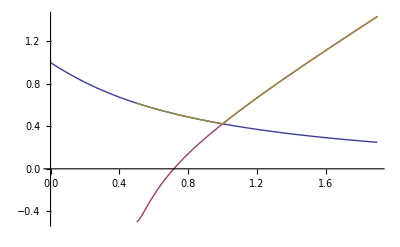

```mathematica
t=0.9;Plot[{(l[x,t]+s[x,t])/2,l[x,t],s[x,t],Max[s[x,t],l[x,t]]},{x,0.5005,3},PlotRange->All]
```

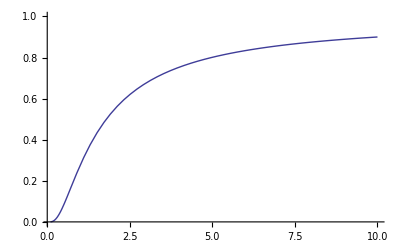

```mathematica
Plot[l[1/x,2],{x,0.1,10},PlotRange->{0,1}]
```

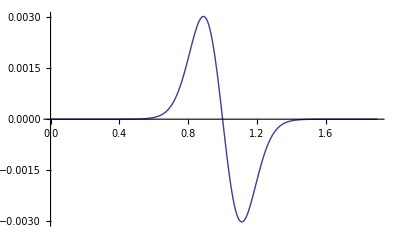

```mathematica
t=0.05;Plot[{-f[x,t]+f[2-x,t]+1-x},{x,0,1.9},PlotRange->All]
```